# “Hump-backed plateau”

Make sure you set the pathpackage below to your current package directory

```mathematica
pathpackage="/Users/gianmicheleinnocenti/Desktop/parton-shower-simulator";
Clear[kernelpath,notebookpath];
kernelpath = StringJoin[pathpackage,"/Kernel"];
resultspath = StringJoin[pathpackage,"/Notebooks/plots"];
pathmain = StringJoin[kernelpath,"/PartonShowerMCFull.wl"]
SetDirectory[kernelpath];
<<"PartonShowerMCFull.wl"
SilentErrors[]; SetStandardSeeds[];
```

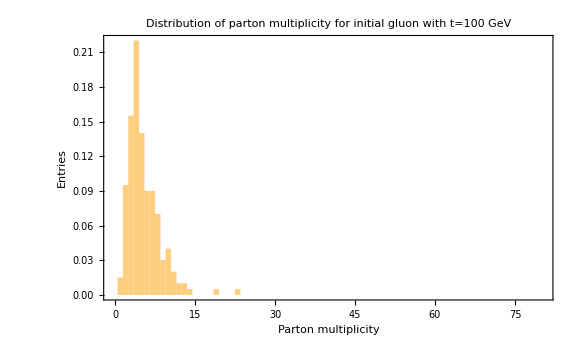
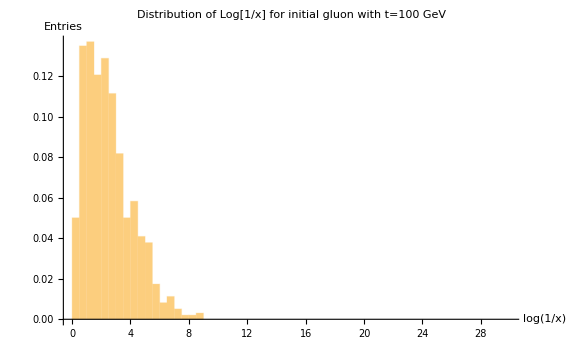
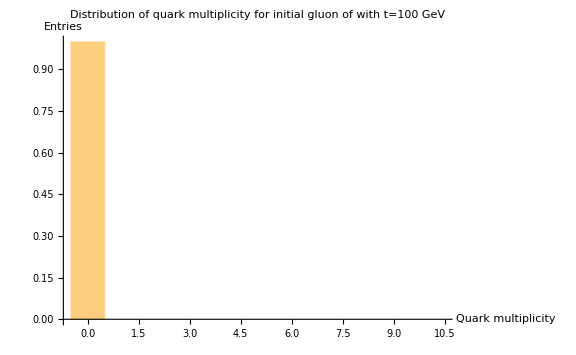
/Users/gianmicheleinnocenti/Desktop/parton-shower-simulator/Notebooks/plots/plotsNTonlygtogg_histolog1overz_maxevents200_tscalecutoff1.0_scale100GeVc.pdf /Users/gianmicheleinnocenti/Desktop/parton-shower-simulator/Notebooks/plots/plotsNTonlygtogg_histomultinit_maxevents200_tscalecutoff1.0_scale100GeVc.pdf /Users/gianmicheleinnocenti/Desktop/parton-shower-simulator/Notebooks/plots/plotsNTonlygtogg_histonquarks_maxevents200_tscalecutoff1.0_scale100GeVc.pdf -Graphics- -Graphics- -Graphics-

```mathematica
resultspath = StringJoin[pathpackage,"/Notebooks/plots/plotsNTonlygtogg_"];
RunShowerMulti[200,200,1.,SudakovPgtoggvacuumNT,SudakovPgtoqqbarvacuumLT,PgtoggvacuumNT,PgtoqqbarvacuumLT,0,200,resultspath]
```